```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],"NewStalliteImages",folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["Zoom"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		fileNames
	]
```

```mathematica
trainingData = associateFilesToGeoRange[getFileNames["training"]];
validationData = associateFilesToGeoRange[getFileNames["validation"]];
```

```mathematica
testData = associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
trainingDataGeo = MapAt[getGeoRange,trainingData,{All,2}];
validationDataGeo = MapAt[getGeoRange,validationData,{All,2}];
```

```mathematica
testDataGeo = MapAt[getGeoRange,testData,{All,2}];
```

```mathematica
trainingDataAsso =AssociationThread[trainingDataGeo[[All,1]],trainingDataGeo[[All,2]]];
validationDataAsso  = AssociationThread[validationDataGeo[[All,1]],validationDataGeo[[All,2]]];
```

```mathematica
testDataAsso = AssociationThread[testDataGeo[[All,1]],testDataGeo[[All,2]]];
```

```mathematica
trainingDataSmall = TakeSmallest[trainingDataAsso,200];
validationDataSmall  = TakeSmallest[validationDataAsso,40];
```

```mathematica
testDataSmall = TakeSmallest[testDataAsso,10];
```

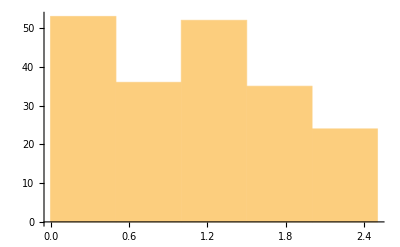

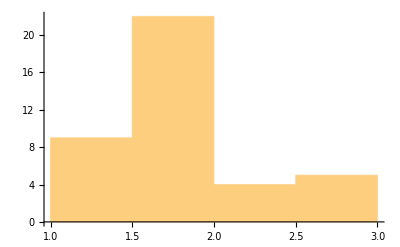

```mathematica
Histogram[trainingDataSmall//Values]
Histogram[validationDataSmall//Values]
```

```mathematica
Values[validationDataSmall]
```

{1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.25062,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.51773,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.70538,1.87592,1.87592,1.87592,1.87592,2.27659,2.27659,2.27659,2.27659,2.55807,2.55807,2.55807,2.55807,2.68925}

```mathematica
ClearAll[tnet]
tnet = Import[File["/Users/mehmetsahin/Downloads/2017-12-27T18-42-44_0_0123_05898_3.71e-3_9.47e-2.wlnet"]];
```

```mathematica
choppedTNet = NetTake[tnet,1]
```

NetChain[<>]

```mathematica
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[1000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
netJoin = NetJoin[choppedTNet,finalLayers]
```

NetChain[<>]

```mathematica
Normal[trainingDataSmall][[1]]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/training/ODpBAi1TBVBvaW50wSMBAqa1VDPJUEBAY5~8smxZWMAtUwRab29tcvJvGxX1MkE~/ODpBAi1TBFpvb21yQpUkHJzuJj8tUwZOdW1iZXJDAg==.png]→0.209949

```mathematica
trainFeatures = MapAt[choppedTNet,Normal[trainingDataSmall],{All,1}];
validFeatures = MapAt[choppedTNet,Normal[validationDataSmall],{All,1}];
```

```mathematica
lastLayerTrain = NetTrain[finalLayers,trainFeatures,ValidationSet->validFeatures];
```

```mathematica
(*newTrainedNet = NetTrain[netJoin,Normal[trainingDataSmall],ValidationSet->Normal[validationDataSmall]];*)
```

```mathematica
lastLayerJoin = NetJoin[choppedTNet,lastLayerTrain]
ClearAll[testData]
testData = associateFilesToGeoRange[getFileNames["testing"]];
```

NetChain[<>]

```mathematica
testDataSmall[[1;;3]]
Map[Import,Take[Keys[testDataSmall],3]]
```

<|File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDCQ==.png]→2.68885,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDBA==.png]→2.68885,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAi71~IKAaEBAHdiVA+JcWMAtUwRab29tcuWtsquqiHs~/ODpBAi1TBFpvb21ymB53chxbYj8tUwZOdW1iZXJDBw==.png]→2.68885|>

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
lastLayerJoin[-Graphics-]
```

2.13191

```mathematica
testData = RandomSample[testData,10];
testData[[1]]
testData[[1,1]]//Import
lastLayerJoin[%]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NewStalliteImages/testing/ODpBAi1TBVBvaW50wSMBAvyTEqGqskJApCzmbtd2XsAtUwRab29tcqi6igelDec~/ODpBAi1TBFpvb21yqLqKB6UN5z8tUwZOdW1iZXJDAQ==.png]→0.720416

-Graphics-

1.99816

```mathematica
newTrainedNet[-Graphics-]
```

0.00566312

```mathematica
Export[FileNameJoin[{"/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/NeuralNets","amazonTrainedNet.wlnet"}],newTrainedNet];
```

```mathematica
(Abs[newTrainedNet[trainingData[[All,1]]]-trainingData[[All,2]]])/trainingData[[All,2]]//Mean
```

1.73789

```mathematica
(Abs[newTrainedNet[testData[[All,1]]]-testData[[All,2]]])/testData[[All,2]]//Mean
```

1.31642

```mathematica
Abs[newTrainedNet[testData[[All,1]]]-testData[[All,2]]]//Mean
```

0.0635155